```mathematica
basedir="d:\\data\\cycle 192\\exp_3-16-13\\rawdata\\sc\\"
Get[basedir<>"camera_ifg.m"]
minIntens=2000;  (* Schwellenwert zur Unterdrückung schwach beleuchtetet Randbereiche der Kamera *)
(*
loadimage[basedir<>filename]    liefert Array mit den einzelnen Bildern aus der Tiff-Datei.;
fittile[images_,tileDX_,tileDY_,nx_,ny_,minIntensity_,period_]

*)
```

d:\data\cycle 192\exp_3-16-13\rawdata\sc\

```mathematica
reduceSlotsBy[img_,its_,slotmax_]:=Module[{maxph,maxtim},
maxtim=slotmax/its;
maxph=Length[img]/(slotmax+2);
Flatten[Table[    Join[{img[[1+(ph-1)*(slotmax+2)]]},Table[Total[img[[(ph-1)*(slotmax+2)+1+(tim-1)*its;;(ph-1)*(slotmax+2)+tim*its]],1],{tim,1,maxtim}],{img[[ph*(slotmax+2)]]}]     ,{ph,1,maxph}],1]
]
```

# Kaiser IFM

```mathematica
filename = "ifg_02Mar1245.tif";
```

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
```

{32,64,64}

```mathematica
Dimensions[img]
```

{32,64,64}

```mathematica
ArrayPlot[img[[2]],ColorFunction->GrayLevel]
```

-Graphics-

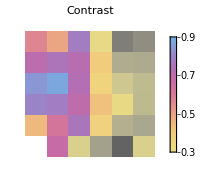
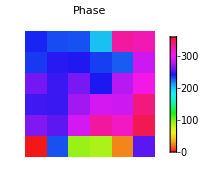
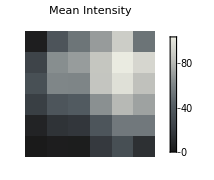
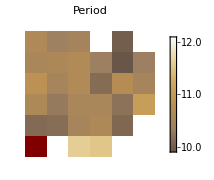

```mathematica
res=fitgrid[img,10,10,1,11];
plotres[res]
```

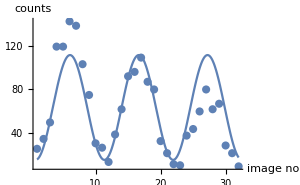
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 63.6118 | 4.43527 | 14.3423 | 1.99166×10^-14
CameraIfgPackage`Private`b | -47.6811 | 6.148 | -7.75556 | 1.89741×10^-8
CameraIfgPackage`Private`c | 0.594311 | 0.014061 | 42.2665 | 6.53729×10^-27
CameraIfgPackage`Private`d | -2.03921 | 0.248394 | -8.20958 | 6.17751×10^-9contr=0.749564
offs=63.6118
phase=243.162°
period=10.5722

```mathematica
showtileres[res,1,4]
```

```mathematica
filename = "ifg_02Mar1518.tif";
```

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
```

{32,64,64}

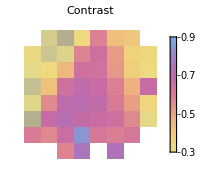
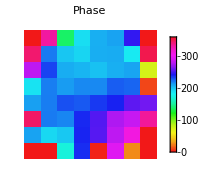
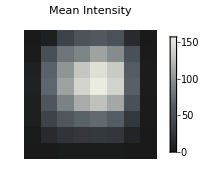
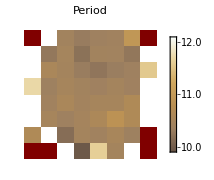

```mathematica
res=fitgrid[img,8,8,8,11];
plotres[res]
```

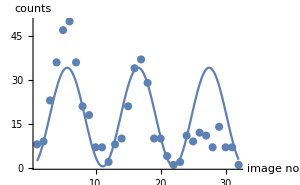
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 17.3233 | 2.0751 | 8.34819 | 4.40905×10^-9
CameraIfgPackage`Private`b | -16.8356 | 2.88662 | -5.83228 | 2.87653×10^-6
CameraIfgPackage`Private`c | 0.575908 | 0.0174169 | 33.066 | 5.53833×10^-24
CameraIfgPackage`Private`d | -1.67864 | 0.302221 | -5.55434 | 6.11084×10^-6contr=0.971846
offs=17.3233
phase=263.821°
period=10.9101

```mathematica
showtileres[res,1,4]
```

```mathematica
filename = "ifg_02Mar1558.tif";
```

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
```

{29,64,64}

```mathematica
res=fitgrid[img,8,8,8,11];
plotres[res]
```

-Graphics--Graphics--Graphics--Graphics-

```mathematica
filename = "ifg_02Mar1650.tif";
```

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
```

{32,64,64}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit :: sszero will be suppressed during this calculation.

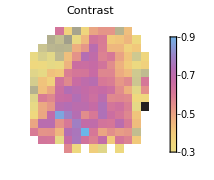
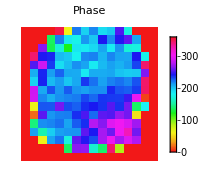
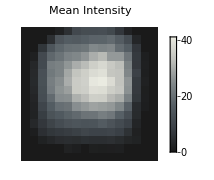
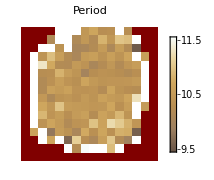

```mathematica
res=fitgrid[img,4,4,8,10.5];
plotres[res]
```

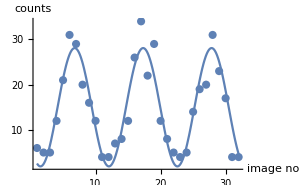
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 15.0141 | 0.731639 | 20.5212 | 2.06359×10^-18
CameraIfgPackage`Private`b | 13.0738 | 1.00417 | 13.0196 | 2.12462×10^-13
CameraIfgPackage`Private`c | 0.596901 | 0.00857412 | 69.6166 | 6.38084×10^-33
CameraIfgPackage`Private`d | -2.48194 | 0.163562 | -15.1743 | 4.88735×10^-15contr=0.870769
offs=15.0141
phase=217.795°
period=10.5263

```mathematica
showtileres[res,4,5]
```

```mathematica
filename = "ifg_03Mar0957.tif";
```

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
```

{32,64,64}

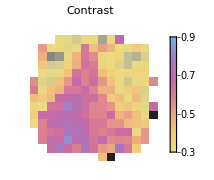
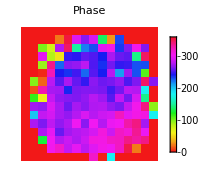
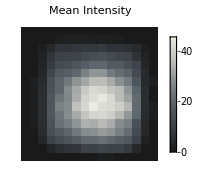
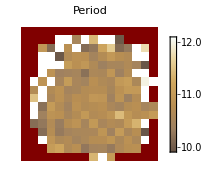

```mathematica
res=fitgrid[img,4,4,8,11];
plotres[res]
```

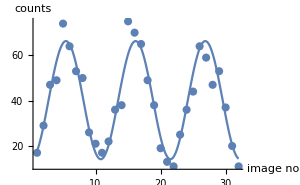
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 40.22 | 1.22895 | 32.727 | 7.33922×10^-24
CameraIfgPackage`Private`b | 26.0573 | 1.7071 | 15.2641 | 4.21541×10^-15
CameraIfgPackage`Private`c | 0.586741 | 0.00696067 | 84.2937 | 3.08541×10^-35
CameraIfgPackage`Private`d | -1.62639 | 0.127787 | -12.7273 | 3.67103×10^-13contr=0.647869
offs=40.22
phase=266.815°
period=10.7086

```mathematica
showtileres[res,7,7]
```

```mathematica
filename = "ifg_03Mar1049.tif";
```

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
```

{32,64,64}

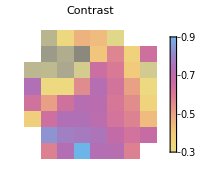
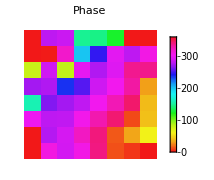
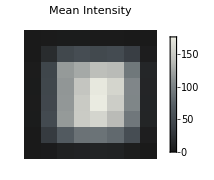
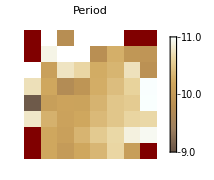

```mathematica
res=fitgrid[img,8,8,16,10];
plotres[res]
```

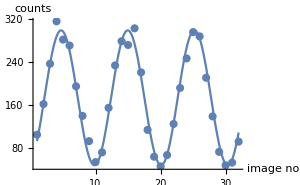
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 173.667 | 3.03153 | 57.2869 | 1.44283×10^-30
CameraIfgPackage`Private`b | 125.486 | 4.31255 | 29.0977 | 1.80057×10^-22
CameraIfgPackage`Private`c | 0.613084 | 0.0035656 | 171.944 | 6.89148×10^-44
CameraIfgPackage`Private`d | -1.31089 | 0.0639693 | -20.4924 | 2.14128×10^-18contr=0.722565
offs=173.667
phase=284.892°
period=10.2485

```mathematica
showtileres[res,4,4]
```

```mathematica
filename = "ifg_04Mar2104.tif";
```

with Indium in path 1

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
```

{20,64,64}

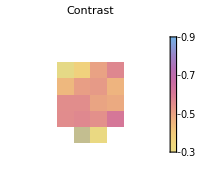
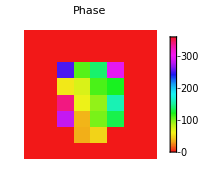
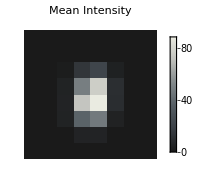
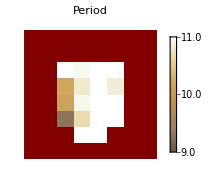

```mathematica
res=fitgrid[img,8,8,16,10];
plotres[res]
```

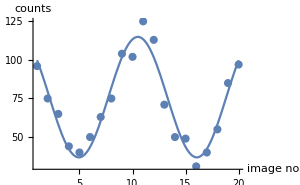
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 75.8784 | 1.91972 | 39.5258 | 2.20055×10^-17
CameraIfgPackage`Private`b | 39.0401 | 2.68828 | 14.5223 | 1.24019×10^-10
CameraIfgPackage`Private`c | 0.565355 | 0.0106052 | 53.309 | 1.90031×10^-19
CameraIfgPackage`Private`d | 1.91692 | 0.126708 | 15.1287 | 6.72149×10^-11contr=0.514508
offs=75.8784
phase=109.832°
period=11.1137

```mathematica
showtileres[res,4,4]
```